# Neural Networks

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

### Single Layer Neural Networks

#### Learning “y=0”

Define a single layer neural network, with a single (scalar) input and a single (scalar) output:

```mathematica
net=NetChain[{DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"]}]
```

NetChain[]

Initialize the neural network with random values

```mathematica
net=NetInitialize[net]
```

NetChain[]

Take a look at the layer, as it is right now:

```mathematica
layer=NetExtract[net,1];
{NetExtract[layer,"Weights"],NetExtract[layer,"Biases"]}
```

{{{-0.0831522}},{0.}}

Generate some random test data, all of the form x→0:

```mathematica
data=Table[x->0,{x,RandomReal[1,10000]}];
```

Look at a few entries in the test data:

```mathematica
RandomSample[data,5]
```

{0.320985→0,0.511507→0,0.119052→0,0.134459→0,0.191648→0}

Learn from the test data

```mathematica
result=NetTrain[net,data]
```

NetChain[]

As expected, result[x] is now always returning 0:

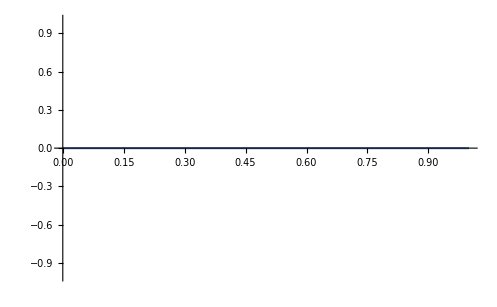

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{-1,1}}]
```

Or something close to zero:

```mathematica
result[0.4]
```

1.74036×10^-6

The weights and biases should also be zero in this simplest possible case:

```mathematica
layer=NetExtract[result,1]
```

None

```mathematica
NetExtract[layer,"Weights"]
```

{{-0.0000120117}}

```mathematica
NetExtract[layer,"Biases"]
```

{6.54506×10^-6}

#### Learning “y=x”

Slightly more complicated: train a single layer neural network on the relationship y=x. First set up the neural network as before:

```mathematica
net=NetChain[{DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"]}];
```

And initialize it again:

```mathematica
net=NetInitialize[net];
```

Define the training data, here the rule is x→x:

```mathematica
data=Table[x->x,{x,RandomReal[1,10000]}];
```

Here is a sample of the training data:

```mathematica
RandomSample[data,5]//Column
```

0.424853→0.424853
0.0396914→0.0396914
0.468508→0.468508
0.82764→0.82764
0.00952728→0.00952728

And train the neural network with the training data, the loss function goes to zero very quickly:

```mathematica
result=NetTrain[net,data];
```

Plot the result, using the the trained function:

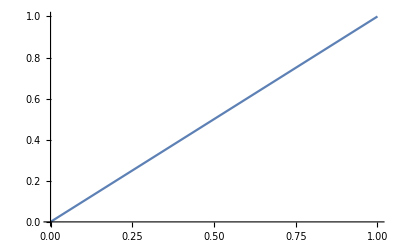

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,1}}]
```

In this case the weight should be 1 (also the slope of this function) and the bias should be 0 (also the intercept of this function):

```mathematica
layer=NetExtract[result,1]
```

None

Here the weight is indeed close to 1:

```mathematica
NetExtract[layer,"Weights"]
```

{{0.999829}}

And the bias is close to 0:

```mathematica
NetExtract[layer,"Biases"]
```

{0.0000910422}

#### Learning “y=2x+1”

One more linear example, in the most general sense: y=a*x+b (here a is 2 and b is 1). Set up the same network again:

```mathematica
net=NetChain[{DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"]}];
```

And initialize it:

```mathematica
net=NetInitialize[net];
```

And prepare the test data for the neural network again:

```mathematica
data=Table[x->2x+1,{x,RandomReal[1,10000]}];
```

Let’s take a look at the test data:

```mathematica
RandomSample[data,5]//Column
```

0.282855→1.56571
0.755509→2.51102
0.192058→1.38412
0.383658→1.76732
0.0835804→1.16716

And train with this test data:

```mathematica
result=NetTrain[net,data];
```

The result should be close to the function 2x+1:

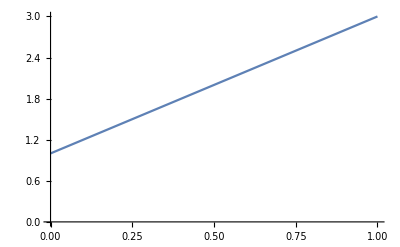

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,3}}]
```

In this case the weight should be 2 (also the slope) and the bias should be close to 1 (the intercept):

```mathematica
layer=NetExtract[result,1]
```

None

```mathematica
NetExtract[layer,"Weights"]
```

{{1.99995}}

```mathematica
NetExtract[layer,"Biases"]
```

{1.00003}

#### Learning “y=x^2”

In this case the single linear ‘DotPlusLayer’ is not going to be able to adequately model the function y=x^2. Simply because there is nothing to make it nonlinear. But let’s try it anyway:

```mathematica
net=NetChain[{DotPlusLayer[1,"Input"->"Scalar","Output"->"Scalar"]}];
```

```mathematica
net=NetInitialize[net];
```

Here use x^2 for the training data:

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

And let’s take a look at a random sample:

```mathematica
RandomSample[data,5]//Column
```

0.158758→0.0252041
0.255149→0.0651011
0.0530423→0.00281349
0.731843→0.535595
0.591321→0.349661

Train the data and hope for the best, even though this probably won’t work:

```mathematica
result=NetTrain[net,data];
```

And check the results

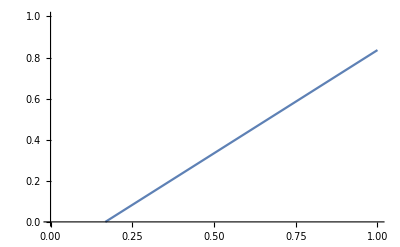

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,1}}]
```

As expected the single linear feedforward network is only going to get a line (linear result).

### Multi Layer Neural Network (single input, single output, with nonlinear layers)

Adding in a second nonlinear layer may improve the neural network result.

#### Learning “y=x^2”

Here add a nonlinear hyperbolic Tan function, so see how the results improve:

```mathematica
net=NetChain[{
DotPlusLayer[1,"Input"->"Scalar"],
ElementwiseLayer[Tanh,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

```mathematica
result=NetTrain[net,data]
```

NetChain[]

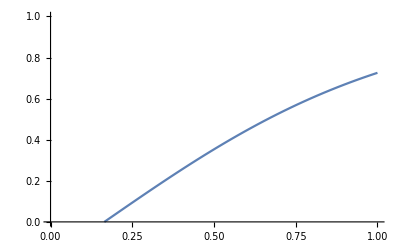

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,1}}]
```

#### Learning “y=x^2”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->"Scalar"],
ElementwiseLayer[Tanh],
DotPlusLayer[1,"Output"->"Scalar"]
}]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

```mathematica
RandomSample[data,5]//Column
```

0.364281→0.132701
0.281609→0.0793037
0.415612→0.172733
0.877892→0.770694
0.909661→0.827483

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->200]
```

NetChain[]

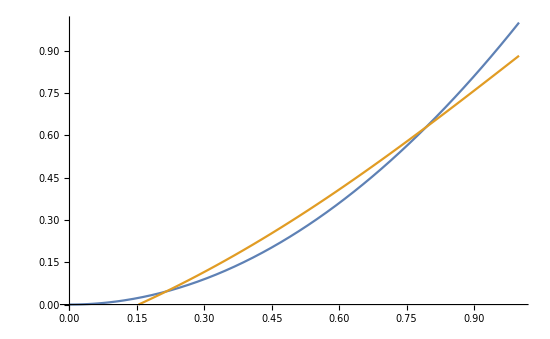

```mathematica
Plot[{x^2,result[x]},{x,0,1},PlotRange->{{0,1},{0,1}}]
```

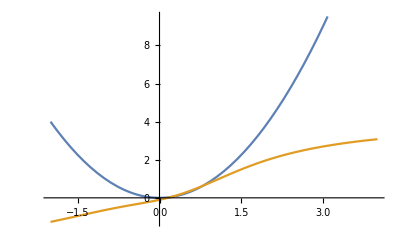

```mathematica
Plot[{x^2,result[x]},{x,-2,4}]
```

#### Learning “y=x^2”

```mathematica
net=NetChain[{
DotPlusLayer[2,"Input"->"Scalar"],
ElementwiseLayer[Tanh],
DotPlusLayer[2],
ElementwiseLayer[Tanh],
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x^2,{x,RandomReal[{-2,2},10000]}];
```

```mathematica
RandomSample[data,5]//Column
```

-0.546484→0.298645
-1.41781→2.01017
-1.09133→1.19101
0.865361→0.74885
-0.133849→0.0179155

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->200]
```

NetChain[]

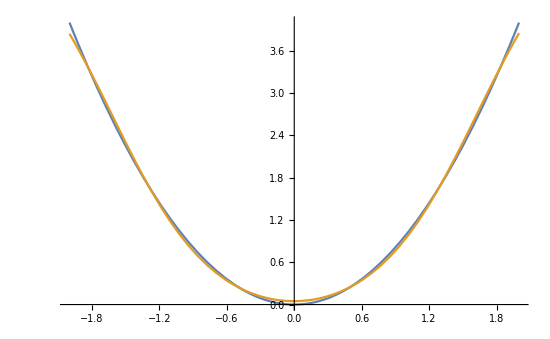

```mathematica
Plot[{x^2,result[x]},{x,-2,2},PlotRange->{{-2,2},{0,4}}]
```

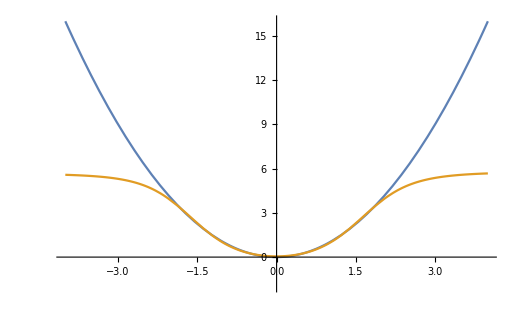

```mathematica
Plot[{x^2,result[x]},{x,-4,4},PlotRange->{{-4,4},{-2,16}}]
```

#### Learning “y=x^3-x”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->"Scalar"],
ElementwiseLayer[Tanh],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x^3-x,{x,RandomReal[{-1,1},10000]}];
```

```mathematica
RandomSample[data,5]//Column
```

-0.821901→0.26669
0.536603→-0.382092
-0.851256→0.234404
-0.878238→0.200851
-0.830126→0.258079

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

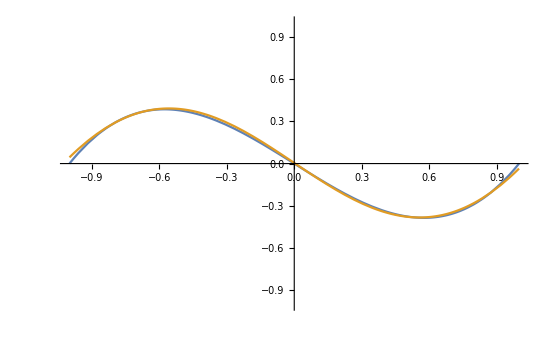

```mathematica
Plot[{x^3-x,result[x]},{x,-1,1},PlotRange->{{-1,1},{-1,1}}]
```

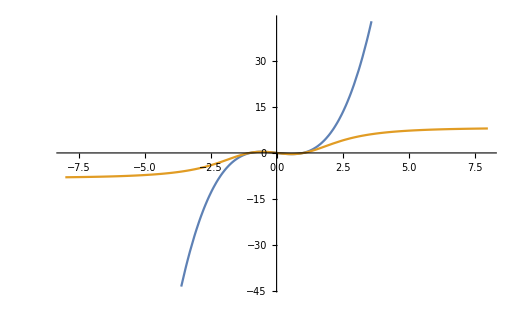

```mathematica
Plot[{x^3-x,result[x]},{x,-8,8}]
```

### Multilayer NN (two inputs, single output)

#### Learning “z=x^2+y^2”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
ElementwiseLayer[Tanh],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->x.x,{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,result[{x,y}]},{x,-1,1},{y,-1,1},Mesh->None]
```

-Graphics3D-

Difference between learned curve and expected curve:

```mathematica
Plot3D[(x^2+y^2)-result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotRange->{Full,Full,{-.01,.01}}]
```

-Graphics3D-

#### Learning “z=Sin[3 x y]”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
Tanh,
10,
Tanh,
DotPlusLayer[1,"Output"->"Scalar"]
}]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Sin[3 First[x] Last[x]],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.481225,-0.711269}→0.855668
{0.864305,-0.376864}→-0.828921
{-0.619433,0.83475}→-0.999808
{0.0119868,-0.0294798}→-0.00106011
{-0.312323,0.536423}→-0.481716

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[3 x y],result[{x,y}]},{x,-1,1},{y,-1,1},Mesh->None]
```

-Graphics3D-

Difference between learned curve and expected curve (error):

```mathematica
Plot3D[(Sin[3 x y])-result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotRange->{Full,Full,{-1,1}}]
```

-Graphics3D-

#### Learning “Sin[3 x y]>0”

```mathematica
net=NetChain[{
DotPlusLayer[10,"Input"->2],
Tanh,
10,
Tanh,
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Boole[Sin[First[x] Last[x]]>0],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.389846,0.394424}→0
{0.414325,-0.192447}→0
{0.599739,-0.690765}→0
{-0.636645,-0.864208}→1
{0.957451,-0.612587}→0

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

#### Learning “Sin[3 x y]>0”

```mathematica
net=NetChain[{
DotPlusLayer[40,"Input"->2],
Ramp,
40,
Ramp,
DotPlusLayer[1,"Output"->"Scalar"]
}];
```

```mathematica
net=NetInitialize[net];
```

```mathematica
data=Table[x->Boole[First[x] Last[x]>0],{x,RandomReal[{-1,1},{10000,2}]}];
```

```mathematica
RandomSample[data,5]//Column
```

{-0.447566,0.938668}→0
{0.449285,-0.967409}→0
{-0.944131,-0.672086}→1
{0.44284,0.775715}→1
{0.795319,-0.0170816}→0

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->250]
```

NetChain[]

```mathematica
Plot3D[result[{x,y}],{x,-1,1},{y,-1,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

### Multilayer NN (multiple inputs, multiple output)

#### 3 inputs to 3 outputs — learning to rotate lists of numbers

```mathematica
net=NetChain[{
DotPlusLayer[40,"Input"->3],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[3,"Output"->3]
}]
```

NetChain[]

```mathematica
net=NetInitialize[net];
```

```mathematica
data=#->RotateLeft[#]&/@RandomInteger[10,{10000,3}];
```

```mathematica
RandomSample[data,4]
```

{{10,3,7}→{3,7,10},{2,2,5}→{2,5,2},{2,2,3}→{2,3,2},{0,10,4}→{10,4,0}}

```mathematica
result=NetTrain[net,data]
```

NetChain[]

```mathematica
result[{2,2,5}]//Round
```

{2,5,2}

```mathematica
result[{1,2,3}]//Round
```

{2,3,1}

```mathematica
result[{8,7,6}]//Round
```

{7,6,8}

#### 20 inputs to 20 outputs — learning to rotate lists of numbers

Set up the neural network:

```mathematica
n=20;
net=NetChain[{
DotPlusLayer[4*n,"Input"->n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[4*n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[n,"Output"->n]
}];
```

Initialize the network with random values:

```mathematica
net=NetInitialize[net];
```

Set up the training data (here, generate lists of integers and rotate them by one element to the left):

```mathematica
data=#->RotateLeft[#]&/@RandomInteger[10,{10000,20}];
```

Train the neural network with the training data

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results of the trained neural network:

```mathematica
Table[
rr=RandomInteger[10,20];
{RotateLeft[rr],Round[result[rr]],SameQ[RotateLeft[rr],Round@result[rr]]}
,10]//Grid[#,Alignment->Left]&
```

{3,9,9,3,1,3,4,7,8,8,7,9,8,9,8,7,0,3,2,4} | {3,9,9,3,1,3,4,7,8,8,7,9,8,9,8,7,0,3,2,4} | True
{5,0,7,7,7,10,9,9,10,6,8,5,5,3,3,3,3,9,0,3} | {5,0,7,7,7,10,9,9,10,6,8,5,5,3,3,3,3,9,0,3} | True
{5,1,4,1,3,2,0,7,3,6,4,6,9,7,8,0,1,0,1,10} | {5,1,4,1,3,2,0,7,3,6,4,6,9,7,8,0,1,0,1,10} | True
{1,4,9,8,0,2,9,10,3,0,5,0,6,8,1,10,3,4,10,10} | {1,4,9,8,0,2,9,10,3,0,5,0,6,8,1,10,3,4,10,10} | True
{10,2,2,7,9,6,6,9,0,2,2,0,2,8,0,10,4,10,8,6} | {10,2,2,7,9,6,6,9,0,2,2,0,2,8,0,10,4,10,8,6} | True
{2,0,2,1,8,0,7,0,5,7,1,1,7,6,7,7,7,3,8,6} | {2,0,2,1,8,0,7,0,5,7,1,1,7,6,7,7,7,3,8,6} | True
{7,4,10,3,4,0,1,4,10,0,7,5,9,5,10,3,7,1,0,10} | {7,4,10,3,4,0,1,4,10,0,7,5,9,5,10,3,7,1,0,10} | True
{7,8,5,0,7,10,7,5,1,1,8,7,1,10,5,4,4,2,6,5} | {7,8,5,0,7,10,7,5,1,1,8,7,1,10,5,4,4,2,6,5} | True
{4,2,9,1,10,5,10,5,6,7,3,6,1,3,10,1,7,9,4,4} | {4,2,9,1,10,5,10,5,6,7,3,6,1,3,10,1,7,9,4,4} | True
{3,0,2,2,1,4,9,4,3,10,5,9,3,6,6,5,1,4,3,3} | {3,0,2,2,1,4,9,4,3,10,5,9,3,6,6,5,1,4,3,3} | True

#### 10 inputs to 10 outputs — learning to rotate lists of numbers

Set up the neural network:

```mathematica
n=10;
net=NetChain[{
DotPlusLayer[4*n,"Input"->n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[4*n],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[n,"Output"->n]
}];
```

Initialize the network with random values:

```mathematica
net=NetInitialize[net];
```

Set up the training data (here, generate lists of integers and rotate them by one element to the left):

```mathematica
data=#->RotateLeft[#,6]&/@RandomInteger[10,{10000,n}];
```

Train the neural network with the training data

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results of the trained neural network:

```mathematica
Table[
rr=RandomInteger[10,n];
{RotateLeft[rr,6],Round[result[rr]],SameQ[RotateLeft[rr,6],Round@result[rr]]}
,10]//Grid[#,Alignment->Left]&
```

{4,2,3,6,9,9,5,6,0,4} | {4,2,3,6,9,9,5,6,0,4} | True
{3,9,0,3,10,4,1,9,8,3} | {3,9,0,3,10,4,1,9,8,3} | True
{2,4,1,2,8,1,0,7,4,1} | {2,4,1,2,8,1,0,7,4,1} | True
{8,3,2,5,10,6,7,5,10,7} | {8,3,2,5,10,6,7,5,10,7} | True
{5,2,5,6,1,4,3,8,9,9} | {5,2,5,6,1,4,3,8,9,9} | True
{7,6,1,5,5,10,5,4,2,9} | {7,6,1,5,5,10,5,4,2,9} | True
{7,8,10,4,8,1,9,3,7,7} | {7,8,10,4,8,1,9,3,7,7} | True
{10,7,9,2,4,5,3,8,9,7} | {10,7,9,2,4,5,3,8,9,7} | True
{3,3,1,5,7,7,6,2,10,6} | {3,3,1,5,7,7,6,2,10,6} | True
{3,2,7,5,0,0,0,9,4,9} | {3,2,7,5,0,0,0,9,4,9} | True

#### Going from 5 variables to 3

Define a nonlinear function from 5 variables (input) to 3 variables  (output):

```mathematica
f[v_List/;(Length[v]===5)]:={v[[1]]+v[[2]]^2,v[[3]]^2+v[[5]],v[[4]]^2}
```

Examples:

```mathematica
f[{1,2,3,4,5}]
```

{5,14,16}

```mathematica
f[{6,4,3,56,3}]
```

{22,12,3136}

Define a neural network that, hopefully, will train to the given function:

```mathematica
net=NetChain[{
DotPlusLayer[75,"Input"->5],
ElementwiseLayer[LogisticSigmoid],
DotPlusLayer[75],
ElementwiseLayer[Tanh],
DotPlusLayer[3,"Output"->3]
}];
```

Initialize the neural network with random variables:

```mathematica
net=NetInitialize[net];
```

Generate a test data set to sample from (to learn from):

```mathematica
data=Table[x->f[x],{x,RandomInteger[10,{10000,5}]}];
```

Some sample data values:

```mathematica
RandomSample[data,10]//Column
```

{9,5,4,1,10}→{34,26,1}
{1,0,9,1,10}→{1,91,1}
{9,10,1,2,6}→{109,7,4}
{5,5,4,1,4}→{30,20,1}
{2,6,9,9,4}→{38,85,81}
{1,0,5,6,8}→{1,33,36}
{10,8,7,9,0}→{74,49,81}
{5,4,6,4,0}→{21,36,16}
{4,3,4,3,9}→{13,25,9}
{1,0,9,1,0}→{1,81,1}

Train the neural network on the given data set:

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->300]
```

NetChain[]

Check the results with a random input:

```mathematica
result[{7,9,4,1,7}]
```

{87.9362,23.1308,1.01788}

The feedforward pass will generate real numbers, but we want integer results (exact) in this case:

```mathematica
Round[result[{7,9,4,1,7}]]
```

{88,23,1}

Expected function value:

```mathematica
f[{7,9,4,1,7}]
```

{88,23,1}

This one is close to the expected result:

```mathematica
Round[result[{7,9,4,1,7}]]===f[{7,9,4,1,7}]
```

True

```mathematica
EuclideanDistance[f[{7,9,4,1,7}],result[{7,9,4,1,7}]]
```

0.146628

Check some more random examples, better results than before with a larger neural network:

```mathematica
Map[
{#,Round[result[#]],f[#],Round[result[#]]===f[#]}&,
RandomInteger[10,{20,5}]
]//Grid
```

{9,5,4,8,7} | {34,23,64} | {34,23,64} | True
{5,3,9,2,1} | {14,82,4} | {14,82,4} | True
{3,5,5,8,2} | {28,27,64} | {28,27,64} | True
{6,4,10,8,5} | {22,105,64} | {22,105,64} | True
{2,1,3,8,10} | {3,19,64} | {3,19,64} | True
{0,1,6,2,3} | {1,39,4} | {1,39,4} | True
{10,3,1,7,7} | {19,8,49} | {19,8,49} | True
{7,7,1,6,4} | {56,5,36} | {56,5,36} | True
{4,4,5,0,9} | {20,34,0} | {20,34,0} | True
{9,0,0,4,5} | {9,5,16} | {9,5,16} | True
{7,6,2,4,3} | {43,7,16} | {43,7,16} | True
{4,9,9,4,7} | {85,88,16} | {85,88,16} | True
{4,0,9,5,5} | {4,86,25} | {4,86,25} | True
{6,8,0,10,9} | {70,9,100} | {70,9,100} | True
{0,0,5,5,0} | {0,25,25} | {0,25,25} | True
{8,8,1,7,9} | {72,10,49} | {72,10,49} | True
{1,10,7,9,7} | {101,56,81} | {101,56,81} | True
{4,5,6,2,4} | {29,40,4} | {29,40,4} | True
{3,1,7,7,9} | {4,58,49} | {4,58,49} | True
{0,5,1,8,6} | {25,7,64} | {25,7,64} | True